```mathematica
y=.
```

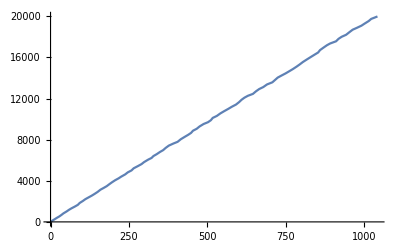

2.53876+4.87929 z

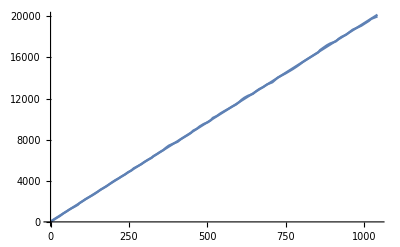

```mathematica
x=.;y=.;
limit=1000;
y=Table[Sum[SquaresR[2,n^2+1],{n,1,m}],{m,3,limit,10}];
x=Table[Length[Solve[a^2+b^2==c^2+1 &&a≤b &&b≤c&&a>0 && a+b+c≤m,{a,b,c},Integers]],{m,3,limit,10}];
ms=Table[i,{i,3,limit,10}];
data=Transpose@{x,y};
ListLinePlot[data]
ms=Table[i,{i,3,limit}];
data2=Transpose@{x,y};
line=Fit[data2,{1,z},z];
2.538756630167393+4.879288746535378 z
Show[ListLinePlot[data2],Plot[line,{z,3,Max[x]}]]
```

```mathematica
ListLinePlot[data]
```

-Graphics-

```mathematica
Part[y,50]/Part[x,50]
```

4532/233

```mathematica
N[4532/233]
```

19.4506

```mathematica
N[9996/521]
```

19.1862

```mathematica
Length[b]
```

20

```mathematica
Table[Length[Solve[a^2+b^2==c^2+1  &&a==53&&b≥a&&c≥b&&  a+b+c<m,{b,c},Integers]],{m,1,10}]
```

5

```mathematica
Solve[a^2+b^2==c^2+1  &&a==45&&b≥a&&c≥b&&  b+c<25000000-a,{b,c},Integers]
```

{{b→ConditionalExpression[251,a==45],c→ConditionalExpression[255,a==45]},{b→ConditionalExpression[505,a==45],c→ConditionalExpression[507,a==45]}}

0,0,1,1,1,1,2,1,2,2,1,2,3,2,3,3,1,3,3,2,3,4,2,4,4,2,3,5,1,6,3,3,5,4,3,4,3,4,3,7,1,5,5,2,5,6,2,8,4,4,3,5

WolframAlphaQueryResults

```mathematica
Paramet
```

```mathematica
Solve[Mod[r^2,5]==4 && r<100,{r}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Mod[r^2,5]==4&&r<100,{r}]

```mathematica
Mod[9,5]
```

4

1,5,4,13,12

WolframAlphaQueryResults